```mathematica
SetDirectory[NotebookDirectory[]];
```

## Growth factor

```mathematica
outputs=Import["../data/growth_factor_unimodal_outputs.csv"];
```

```mathematica
fSplit[vData__,aLen_Integer]:=Table[vData[[(1 + (i-1) aLen);;i aLen,All]],{i,1,(Length@vData)/aLen,1}]
fPostWarmup[splitData__]:=Block[{aLen=Length@splitData[[1]]},Table[splitData[[i]][[aLen/2;;]],{i,1,Length@splitData,1}]]
```

```mathematica
test=fSplit[outputs,10000];
test = Flatten[fPostWarmup[test],1];
dist1=SmoothKernelDistribution[test[[All,1]],100];
dist2=SmoothKernelDistribution[test[[All,2]],100];
```

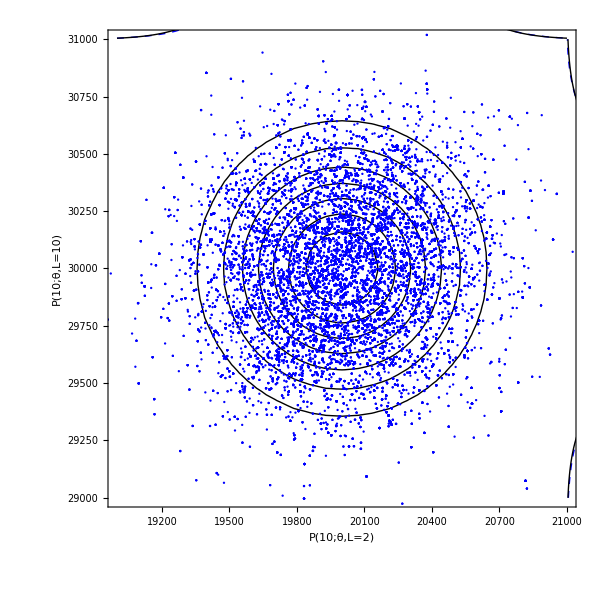
-Graphics-A.

```mathematica
gUniform=Labeled[Show[ContourPlot[PDF[MultinormalDistribution[{2 10^4,3 10^4},10^5 IdentityMatrix[2]],{x,y}],{x,19000,21000},{y,29000,31000},ContourShading->None,PlotRangePadding->0,PlotRangeClipping->False,ImagePadding->{{120,120},{40,120}},Frame->True,FrameLabel->{"P(10;θ,L=2)","P(10;θ,L=10)"},LabelStyle->{Black,FontSize->14},FrameStyle->Black,Epilog->{{Blue,Dashed,Line[Table[{x,31000+500000 PDF[dist1,x]},{x,19000,21000,20}]]},{Black,Line[Table[{x,31000+500000PDF[NormalDistribution[2 10^4, Sqrt[10^5]],x]},{x,19000,21000,20}]]},{{Dashed,Blue,Line[Table[{21000+500000PDF[dist2,x],x},{x,29000,31000,20}]]},{Black,Line[Table[{21000+500000PDF[NormalDistribution[3 10^4,Sqrt[10^5]],x],x},{x,29000,31000,20}]]}}}],ListPlot[test,PlotRange->{{19000,21000},{29000,31000}},PlotStyle->Blue],ImageSize->600],"A.",{{Top,Left}},LabelStyle->{Black,FontSize->18}]
```

```mathematica
inputs=Import["../data/growth_factor_unimodal_inputs.csv"];
```

```mathematica
test1=fSplit[inputs,10000];
test1 = Flatten[fPostWarmup[test1],1];
```

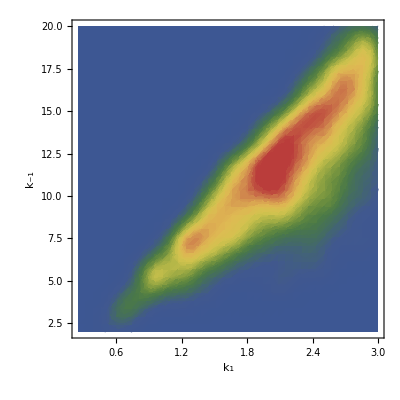
-Graphics-A.

```mathematica
gUniformInput=Labeled[SmoothDensityHistogram[test1[[All,{3,4}]],Mesh->20,MeshStyle->Directive[Gray,Dashed],ColorFunction->"DarkRainbow",PlotRange->{{0.25,3},{2,20}},Frame->{True,True,False,False},FrameLabel->{"k_1","k_-1"},FrameStyle->Black,LabelStyle->{Black,FontSize->14},ImageSize->400],"A.", {{Top, Left}},LabelStyle->{Black,FontSize->18}]
```

```mathematica
summary1=Transpose@{Quantile[#,0.025],Median[#],Quantile[#,0.975]}&@test1;
summary1=Round[summary1,0.01];
```

```mathematica
Grid@summary1
```

441006. | 606439. | 772484.
0.2 | 0.4 | 0.49
0.89 | 2.16 | 2.95
4.35 | 11.23 | 18.71
0.01 | 0.02 | 0.03

## Growth factor (non-uniform)

```mathematica
inputs=Import["../data/growth_factor_nonuniform_inputs.csv"];
```

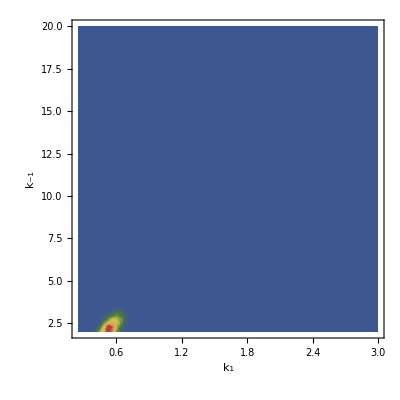
-Graphics-B.

```mathematica
test2=fSplit[inputs,10000];
test2 = Flatten[fPostWarmup[test2],1];
gNonuniformInput=Labeled[SmoothDensityHistogram[test2[[All,{3,4}]],Mesh->10,MeshStyle->Directive[Gray,Dashed],ColorFunction->"DarkRainbow",PlotRange->{{0.25,3},{2,20}},Frame->{True,True,False,False},FrameLabel->{"k_1","k_-1"},FrameStyle->Black,LabelStyle->{Black,FontSize->14},ImageSize->400],"B.", {{Top, Left}},LabelStyle->{Black,FontSize->18}]
```

```mathematica
outputs=Import["../data/growth_factor_nonuniform_outputs.csv"];
```

```mathematica
test=fSplit[outputs,10000];
test = Flatten[fPostWarmup[test],1];
dist1=SmoothKernelDistribution[test[[All,1]],100];
dist2=SmoothKernelDistribution[test[[All,2]],100];
```

```mathematica
SmoothKernelDistribution
```

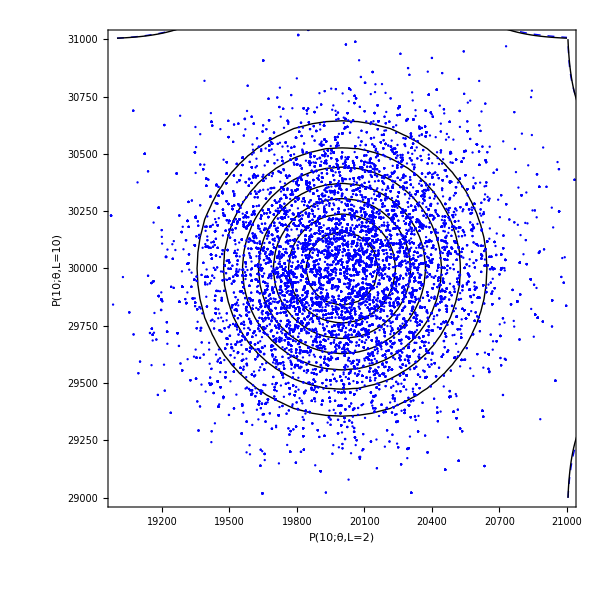
-Graphics-B.

```mathematica
gNonuniform=Labeled[Show[ContourPlot[PDF[MultinormalDistribution[{2 10^4,3 10^4},10^5 IdentityMatrix[2]],{x,y}],{x,19000,21000},{y,29000,31000},PlotRange->{{19000,21000},{29000,31000}},ContourShading->None,PlotRangePadding->0,PlotRangeClipping->False,ImagePadding->{{120,120},{40,120}},Frame->True,FrameLabel->{"P(10;θ,L=2)","P(10;θ,L=10)"},LabelStyle->{Black,FontSize->14},FrameStyle->Black,Epilog->{{Blue,Dashed,Line[Table[{x,31000+500000 PDF[dist1,x]},{x,19000,21000,20}]]},{Black,Line[Table[{x,31000+500000PDF[NormalDistribution[2 10^4, Sqrt[10^5]],x]},{x,19000,21000,20}]]},{{Blue,Dashed,Line[Table[{21000+500000PDF[dist2,x],x},{x,29000,31000,20}]]},{Black,Line[Table[{21000+500000PDF[NormalDistribution[3 10^4,Sqrt[10^5]],x],x},{x,29000,31000,20}]]}}}],ListPlot[test,PlotRange->{{19000,21000},{29000,31000}},PlotStyle->Blue],ImageSize->600],"B.",{{Top,Left}},LabelStyle->{Black,FontSize->18}]
```

```mathematica
gOutput=GraphicsRow[{gUniform,gNonuniform},ImageSize->1300]
```

-Graphics-

```mathematica
Export["../figures/growth_factor_outputs.pdf",gOutput]
```

../figures/growth_factor_outputs.pdf

```mathematica
gInput=GraphicsRow[{gUniformInput,gNonuniformInput},ImageSize->1000]
```

-Graphics-

```mathematica
Export["../figures/growth_factor_inputs.png",gInput,ImageResolution->500]
```

../figures/growth_factor_inputs.png

```mathematica
summary2=Transpose@{Quantile[#,0.025],Median[#],Quantile[#,0.975]}&@test2;
summary2=Round[summary2,0.01];
```

```mathematica
Grid[summary1]
```

441006. | 606439. | 772484.
0.2 | 0.4 | 0.49
0.89 | 2.16 | 2.95
4.35 | 11.23 | 18.71
0.01 | 0.02 | 0.03

```mathematica
Grid@Table[Flatten[Thread[{summary1,summary2}][[i]],1],{i,1,5,1}]//TeXForm
```

\begin{array}{cccccc}
 441006. & 606439. & 772484. & 408396. & 529558. & 678632. \\
 0.2 & 0.4 & 0.49 & 0.22 & 0.33 & 0.46 \\
 0.89 & 2.16 & 2.95 & 0.39 & 0.54 & 0.7 \\
 4.35 & 11.23 & 18.71 & 1.39 & 2.26 & 3.35 \\
 0.01 & 0.02 & 0.03 & 0.02 & 0.02 & 0.03 \\
\end{array}

## Michaelis Menten bimodal

```mathematica
outputs=Import["../data/mm_bimodal_outputs.csv"];
test=fSplit[outputs,10000];
test = Flatten[fPostWarmup[test],1];
dist1=SmoothKernelDistribution[test[[All,1]]];
dist2=SmoothKernelDistribution[test[[All,2]]];
```

```mathematica
mixdist=MixtureDistribution[{0.5,0.5},{MultinormalDistribution[{2.15,1.6},{{0.0184,-0.013},{-0.013, 0.01}}],MultinormalDistribution[{2.8,1.0},{{0.02,-0.01},{-0.01,0.02}}]}];
mixdist1=MarginalDistribution[mixdist,1];
mixdist2=MarginalDistribution[mixdist,2];
```

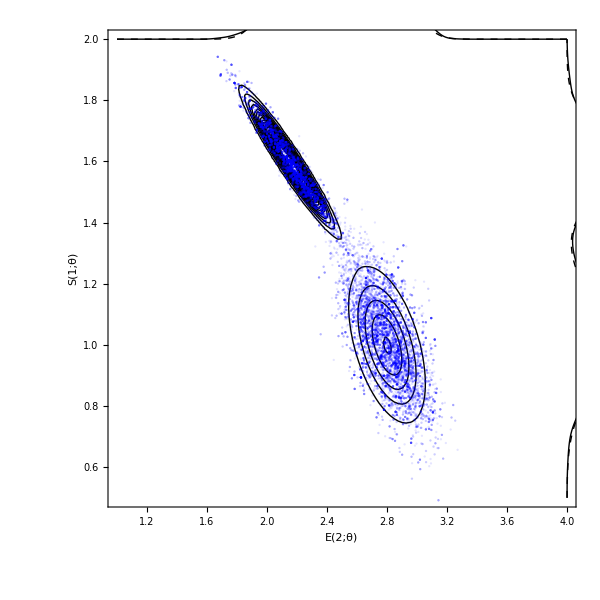

```mathematica
Show[ContourPlot[PDF[MultinormalDistribution[{2.15,1.6},{{0.0184,-0.013},{-0.013, 0.01}}],{x,y}]+PDF[MultinormalDistribution[{2.8,1.0},{{0.02,-0.01},{-0.01,0.02}}],{x,y}],{x,1,4},{y,0.5,2},Frame->True,FrameLabel->{"E(2;θ)","S(1;θ)"},LabelStyle->{Black,FontSize->14},FrameStyle->Black,ContourShading->None,PlotRange->Full,Contours->20,PlotRangePadding->0,PlotRangeClipping->False,ImagePadding->{{50,70},{50,120}},Epilog->{{Black,Dashed,Line[Table[{x,2+0.2 PDF[mixdist1,x]},{x,1,4,0.01}]]},{Black,Dashed,Line[Table[{4+0.2 PDF[mixdist2,x],x},{x,0.5,2,0.01}]]},{Black,Line[Table[{x,2+ 0.2 PDF[dist1,x]},{x,1,4,0.01}]]},{Black,Line[Table[{4+0.2 PDF[dist2,x],x},{x,0.5,2,0.01}]]}}],ListPlot[test,PlotStyle->Opacity[0.1,Blue]],ImageSize->600]
```

```mathematica
inputs=Import["../data/mm_bimodal_inputs.csv"];
testi=fSplit[inputs,10000];
testi = Flatten[fPostWarmup[testi],1];
```

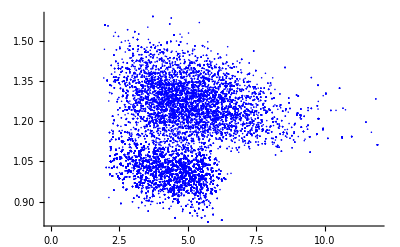

```mathematica
ListPlot[testi[[All,{1,3}]],PlotStyle->Blue]
```

```mathematica
DistanceFunction
```

```mathematica
clusters=FindClusters[testi[[All,{1,3}]],3];
```

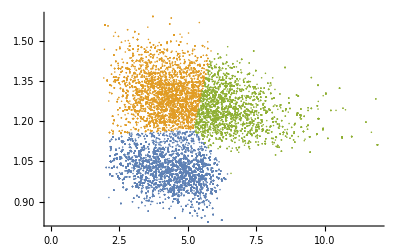

```mathematica
ListPlot[clusters]
```

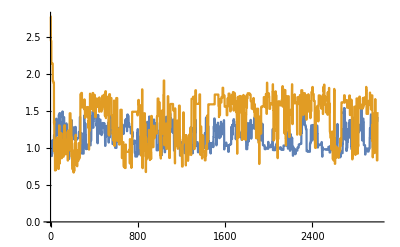

```mathematica
ListLinePlot[{testi[[1;;3000,3]],outputs[[1;;3000,2]]}]
```

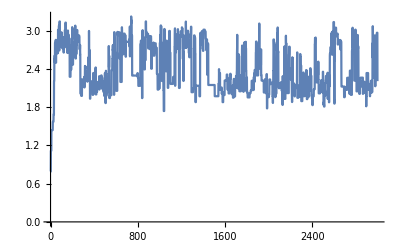

```mathematica
ListLinePlot[outputs[[1;;3000,1]]]
```

## Michaelis Menten 4D